## Functions for modeling

UNITS:
	GPa;
	km;
	s;

### Linear-solid stiffness matrix

cij0[i], Q0[i] are assumed defined for each layer i

```mathematica
cijCarcione[pars_,ω0_,ω_]:=Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i}=pars;

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),ρi}//N

]
```

```mathematica
cijCarcioneCompiled=
Compile[{{cijQρ,_Real, 1},{ω0,_Real},{ω,_Complex}},
Module[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},

c11i=cijQρ[[1]];
c13i=cijQρ[[2]];
c33i=cijQρ[[3]];
c44i=cijQρ[[4]];
ρi=cijQρ[[5]];
Q01i=cijQρ[[6]];
Q02i=cijQρ[[7]];

{(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c33i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c11i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),c13i-(2 c44i ω ((-2+√(1+Q01i^2)+√(1+Q02i^2)) ω+ⅈ (Q01i+Q02i) ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))+c11i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω)+c33i/(-1+√(1+Q01i^2)+(ⅈ Q01i ω0)/ω),(2 c44i ω ((√(1+Q01i^2)-√(1+Q02i^2)) ω+ⅈ (Q01i-Q02i) ω0)+c11i ω ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)+c33i (√(1+Q01i^2) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0))/(((-1+√(1+Q01i^2)) ω+ⅈ Q01i ω0) ((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0)),(c44i (ω+√(1+Q02i^2) ω+ⅈ Q02i ω0))/((-1+√(1+Q02i^2)) ω+ⅈ Q02i ω0),Re@ρi}

],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
cijLS[{c11i_,c13i_,c33i_,c44i_,ρi_,Q01i_,Q02i_},ω0_,ω_]:=cijCarcioneCompiled[{c11i,c13i,c33i,c44i,ρi,Q01i,Q02i},ω0,ω];
```

### Slowness, L1/L2 matrices

Requires run of the cijCarcione function to get frequency-dependent cij[i]

```mathematica
GetLStovasUrsin[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2,req1,req2,imq1,imq2},
α0=√(c33i/ρi);
β0=√(c44i/ρi);
σ0=1-c44i/c33i;
δ=(c13i-c33i+2c44i)/c33i;
η=(c11i c33i-(c13i+2c44i)^2)/(2 c33i^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));


req1=Re[1/α0^2-p^2-p^2 Sα];
req2=Re[1/β0^2-p^2-p^2 Sβ];
imq1=Im[1/α0^2-p^2-p^2 Sα];
imq2=Im[1/β0^2-p^2-p^2 Sβ];
imq1=Sign[imq1]imq1;
imq2=Sign[imq2]imq2;
req1=req1;
req2=req2;

qα=√(req1+ⅈ imq1);
qβ=√(req2+ⅈ imq2);

(*qα=1/α0^2-p^2-p^2 Sα;
qβ=1/β0^2-p^2-p^2 Sβ;*)
(*
qα=Sign[Im[qα]]qα;
qβ=Sign[Im[qβ]]qβ;*)



L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

(*{{qα,qβ},{L1,L2}}*)
{{{qα,0},{0,qβ}},L1,L2}
(*l1[j]=L1//N;
l2[j]=L2//N;
q1[j]=qα//N;
q2[j]=qβ//N;*)

]
```

```mathematica
qLCompiled=
Compile[{{cij,_Complex, 1},{ρi,_Real},{p,_Complex}},
Module[
{L1,L2,d1,d2,d3,d4,d5,qα,qβ,α0,β0,η,δ,σ0,Sα,Sβ,R,R1,R2},
α0=√(cij[[3]]/ρi);
β0=√(cij[[4]]/ρi);
σ0=1-cij[[4]]/cij[[3]];
δ=(cij[[2]]-cij[[3]]+2cij[[4]])/cij[[3]];
η=(cij[[1]] cij[[3]]-(cij[[2]]+2cij[[4]])^2)/(2 cij[[3]]^2);
R1=2(1-p^2 β0^2)(δ+2 p^2 α0^2 η)^2;
R2=σ0+2 p^2 β0^2 δ-2 p^2 α0^2(1-2 p^2 β0^2)η;
R=R1/(R2+√(R2^2+2 p^2 β0^2 R1));
Sα=2δ+2 p^2 α0^2 η+R;
Sβ=2(1-p^2 β0^2)α0^2/β0^2 η-R;

qα=(Re@#+ⅈ Abs@Im@#)&@√(1/α0^2-p^2-p^2 Sα);
qβ=(Re@#+ⅈ Abs@Im@#)&@√(1/β0^2-p^2-p^2 Sβ);
d2=√((σ0+δ)/(σ0+Sα));
d3=2 β0^2(σ0+1/2(Sα+δ))/(σ0+δ);
d4=√((σ0-p^2 β0^2(σ0+Sβ))/((1-p^2 β0^2(1+Sβ))(σ0+δ)));
d5=(σ0-2 p^2 β0^2(σ0+1/2(Sβ+δ)))/(σ0+δ);
d1=1/(√(p^2 d3+d5));
L1=d1{
{d2 √(qα/ρi),1/d4 p/(√(ρi qβ))},
{d3 d2 p √(ρi qα),-d5/d4 √(ρi/qβ)}
};

L2=d1{
{d5/d2 √(ρi/qα),d3 d4 p √(ρi qβ)},
{1/d2 p/(√(ρi qα)),-d4 √(qβ/ρi)}
};

{{{qα,0},{0,qβ}},L1,L2}
],CompilationTarget->"C", RuntimeOptions->"Speed"
];
```

```mathematica
qL[{c11i_, c13i_, c33i_, c44i_, ρi_},p_]:=qLCompiled[{c11i, c13i, c33i, c44i}, ρi,p];
```

### Reflectivity and transmissivity

```mathematica
(*
REFLECTIVITY ONLY
*)
stackRefExperiment2[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray](*;
{transArray,refArray, phaseArray}*)
(*foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
(*;
phaseArray=Exp[ⅈ ω(qABArray d)];
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}]*)
]
```

```mathematica
(*
BOTH REFLECTIVITY AND TRANSMISSIVITY
OUPUT[[1]] IS TRANSMISSIVITY MATRIX
OUPUT[[2]] IS REFLECTIVITY MATRIX
*)
stackRefExperiment2RT[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray, L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,fR,fT},
{qABArray, L1ar, L2ar}=Transpose[qL[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
fR=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
fT=(#1.Inverse[IdentityMatrix[2]+#3.fR[#5,#2,#3,#4]].#2.#4)&;
Fold[
{fT[#1[[1]],#2[[1]],#2[[2]],#2[[3]],#1[[2]]],
fR[#1[[2]],#2[[1]],#2[[2]],#2[[3]]]}&,{{{1,0},{0,1}},{{0,0},{0,0}}},foldArray]
]
```

```mathematica
<<CompiledFunctionTools`
```

```mathematica
stackRefExperiment[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
{CArray,DArray}=Transpose@MapThread[
{Transpose[#1[[2]]].#2[[1]],Transpose[#1[[1]]].#2[[2]]}&,
{RotateLeft@L12Array,L12Array}];
{transArray , refArray}=Transpose@MapThread[{2Transpose@Inverse[#1+#2],Transpose[(#1-#2)].Transpose@Inverse[#1+#2]}&,{CArray, DArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

```mathematica
stackRefTransCoefs[ω_,p_,CijsAndρ:{{_,_,_,_,_}..}, d_List]/;(ArrayQ[d]&&(Length@d==Length@CijsAndρ)):=Module[{qABArray,L1ar,L2ar, L12Array,CArray,DArray,refArray, transArray, phaseArray, foldArray,f},
{qABArray, L1ar, L2ar}=Transpose[GetLStovasUrsin[#,p]&/@CijsAndρ];
L12Array=Transpose@{L1ar, L2ar};
CArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,2]],L12Array[[;;,1]]}];
DArray=MapThread[Transpose[#1].#2&,{RotateLeft@L12Array[[;;,1]],L12Array[[;;,2]]}];
transArray=2Transpose/@ Inverse/@(CArray+DArray);
refArray=1/2 MapThread[#1.#2&,{Transpose/@(CArray-DArray),transArray}];
phaseArray=Exp[ⅈ ω(qABArray d)]-ConstantArray[{{0.,1.},{1.,0.}},Length[d]]//Chop;
foldArray=Reverse@Most@Transpose[{transArray,refArray, phaseArray}];
f=(#4.(#3+Transpose[#2].#1.Inverse[IdentityMatrix[2]+#3.#1].#2).#4)&;
Fold[f[#1,#2[[1]],#2[[2]],#2[[3]]]&,{{0,0},{0,0}},foldArray]
]
```

### Time-domain description

```mathematica
addSrcRec[RT_,ω_,zs_,zr_,qAB1_]:=Module[
{exp},

exp[z_]:=Exp[ⅈ ω z qAB1]-{{0,1},{1,0}};

exp[zr].RT.exp[zs]//N//Chop

]

(*
NOTE THAT RPP IS TAKEN FOR INTEGRATION ([[1,1]] after the StackRefExperiment function)
*)

integrandp[x_,p_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{p0=p},
addSrcRec[
stackRefExperiment2[ω,p0,CijsAndρ, dList],ω,zs,zr,qL[CijsAndρ[[1]],p0][[1]]][[1,1]] BesselJ[0,x p0 ω]p0 ω^2]

integrandk[x_,k_?NumericQ,ω_?NumericQ,CijsAndρ:{{_,_,_,_,_}..},dList_,zs_,zr_]:=With[{k0=1000k},
addSrcRec[
stackRefExperiment2[ω,k0/ω,CijsAndρ, dList],ω,zs,zr,qL[CijsAndρ[[1]],k0/ω][[1]]][[1,1]] BesselJ[0,x k0]k0]
```

### Numerical testing

```mathematica
overburden={vp^2 den,vp^2 den-2 vs^2 den,vp^2 den,vs^2 den,den,500,500}/.vp->2.5/.vs->1.2/.den->1.8;
binarymodel={
(*shale*)
{22.56,12.38,17.35,3.15,2.38,100,50},
(*sandstone*)
{26.73,12.51,26.73,7.11,2.22,150,100}(*,
(*siltstone*)
{60.13,38.26,50.87,17.17,2.18,100,50}*)
};
```

```mathematica
nrep=2;
model=Join[{overburden},Flatten[ConstantArray[binarymodel,{nrep}],1]];
```

```mathematica
SeedRandom[2018];
dList=ArrayPad[RandomReal[{0,1},Length[model]-2],1];
```

```mathematica
ωcomp=2 Pi 40;
ω0=2Pi 150;
```

```mathematica
cijsNum=cijLS[#,ω0,ωcomp ]&/@model;
```

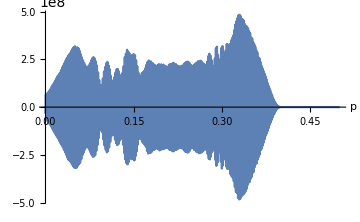
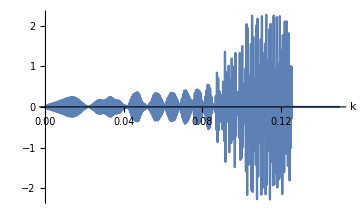

```mathematica
With[{x=10,zs=0.4,zr=0.3,ω=2Pi 50},
{
Plot[
Re@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Re@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

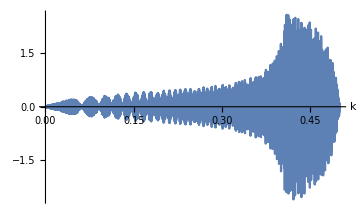
{-Graphics-,-Graphics-}

```mathematica
With[{x=10,zs=0.4,zr=0.3,ω=2Pi 200},
{
Plot[
Im@integrandp[x,p+.005I,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},PlotRange->{Automatic,Full},AxesLabel->Automatic,ImageSize->Medium],
Plot[
Im@integrandk[x,k ,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,.5},PlotRange->{{0,.5},Full},AxesLabel->Automatic,ImageSize->Medium]
}
]
```

```mathematica
With[{x=0,zs=.1,zr=.2,ω=2 Pi 10},
NIntegrate[
integrandp[x,p,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{p,0,.5},Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
]
```

3.55218+2.52026 ⅈ

```mathematica
With[{x=0,zs=.1,zr=.2,ω=2 Pi 10},
NIntegrate[
integrandk[x,k,ω,cijLS[#,ω0,ω]&/@model,dList,zs,zr],{k,0,.5},Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->Infinity,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0124015-0.00255156 ⅈ

### Compute single trace

```mathematica
(*VARIABLE UPPER BOUNDARY FOR INTEGRATION*)
upperB[f_,fm_,p0_,pm_]:=p0+f/fm pm
rickerF[ω_,ωp_]:=(2 ω^2)/(√Pi ωp^3)Exp[-(ω/ωp)^2]//N
```

```mathematica
deltafreq=1;

Monitor[
With[{x=0,zs=.3,zr=.2,ωc=2Pi f,fmax=200,ωricker=2Pi 30,df=deltafreq},
{zeroX,srcF}=Table[{i=
NIntegrate[
integrandk[x,k,ωc,cijLS[#,ω0,ωc]&/@model,dList,zs,zr],{k,0,upperB[f,fmax,.1,.55]},Method->{"GlobalAdaptive","MaxErrorIncreases"->2000},MaxRecursion->20,WorkingPrecision->MachinePrecision,PrecisionGoal->8,AccuracyGoal->Infinity],
rickerF[2Pi f,ωricker]},
{f,1,fmax,df}]//Transpose
]
,{f,i}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in k near {k} = {0.0210942}. NIntegrate obtained 0.00443373-0.00229919 ⅈ and 8.07836×10^-10 for the integral and error estimates.

Set::shape: Lists {zeroX, srcF} and {{-0.00202131 - 0.0000715429\\\ ⅈ, 6.64399×10^-6}, {-0.00015898 + 0.000348095\\\ ⅈ, 0.0000264875}, {-0.00151777 + 0.00169012\\\ ⅈ, 0.0000592667}, {-0.00297368 - 0.00270999\\\ ⅈ, 0.000104547}, {0.00143118 - 0.00270169\\\ ⅈ, 0.000161729}, «42», {-0.0176926 + 0.0317324\\\ ⅈ, 0.00118468}, {-0.0467615 - 0.0112192\\\ ⅈ, 0.00110842}, {0.00851126 - 0.0432914\\\ ⅈ, 0.0010339}, «150»} are not the same shape.

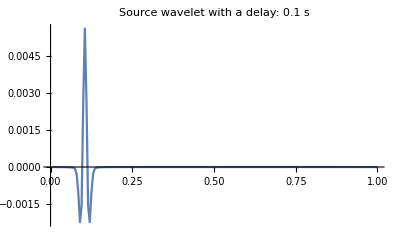

```mathematica
(*time vector*)
t=Range[Length[srcF]]/(deltafreq Length[srcF])//N;

With[{delay=.1},
ListLinePlot[{t,Re@InverseFourier@(srcF (Exp[ⅈ 2Pi# delay]&/@(Range[200]-1)))}ᵀ,PlotRange->{Automatic,Full},PlotLabel->"Source wavelet with a delay: "<>ToString[delay]<>" s"]
]
```

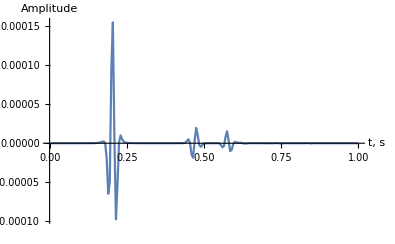

```mathematica
ListLinePlot[{t,Re@InverseFourier@(zeroX srcF)}ᵀ,PlotRange->Full,AxesLabel->{"t, s","Amplitude"}]
```